```mathematica
<<Notation`
Symbolize[Subscript[x_, y_]]
```

```mathematica
Subscript[D, 1]=44 10^-3; (*meters*)
Subscript[D, 2]=60 10^-3 ; (*meters*)
Subscript[D, 3]=30  10^-3; (*meters*)

Subscript[r, 1]=Subscript[D, 1]/2; (*meters*)
Subscript[r, 2]=Subscript[D, 2]/2 ; (*meters*)
Subscript[r, 3]=Subscript[D, 3]/2; (*meters*)

Subscript[J, 1]=(π ((Subscript[r, 2])^4-(Subscript[r, 1])^4))/2 (*meters^4*)//N
Subscript[J, 2]=(π (Subscript[r, 2])^4)/2 (*meters^4*)//N
Subscript[J, 3]=(π (Subscript[r, 3])^4)/2 (*meters^4*)//N
```

9.04377×10^-7

1.27235×10^-6

7.95216×10^-8

```mathematica
ClearAll[J]
J[X_]:=Piecewise[
{{Subscript[J, 1],0≤ X<0.6},
{Subscript[J, 2],0.6≤ X<0.8},
{Subscript[J, 3],0.8≤ X<1.2}}
] (*meters^4*)

T=250; (*In newton.meter *)
G=77 10^9 (*N/m^2 or Pa*);
L=1.2  (*in meters*);
```

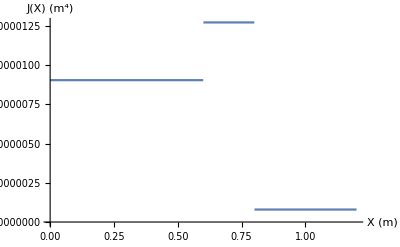

```mathematica
Plot[J[X],{X,0,1.2},AxesLabel->{"X (m)","J(X) (m^4)"}]
```

```mathematica
Subscript[θ, L]=T/G Integrate[1/J[X],{X,0,L}]
```

0.0189958

```mathematica
Subscript[θ, L]/Degree
```

1.08838